```mathematica
SetDirectory["/Users/gerardoalvarez/Desktop/Inelastic Dark Matter"]
```

/Users/gerardoalvarez/Desktop/Inelastic Dark Matter

```mathematica
(* mx, mphi, delta in GeV. velocity in km/s  *)
Sigmacalc[mx_,mphi_,delta_,vel_]:=Module[
(* Parameters *)
{
vlight=299792458/10^3,
mχ=mx,
mϕ=mphi,
δ=delta,
velo=vel
},
Print[velo];
v=velo/vlight;
αχ=(*1/100(mχ/270)*)8/1000; (* Dark Fine Structure Constant *)
b=(αχ mχ)/mϕ; (* Dimensionless parameter. Range of Yukawa potential *)
a=v/(2 αχ); (* Dimensionless parameter ~ momentum of lighter species *)
c=√(a^2-(2δ)/(mχ αχ^2)); (* Dimensionless parameter ~ momentum of heavier species *)
(* Initialize angular momentum mode *)
l=0;
lmax=1500;

(* Initialize scattering cross sections *)
σ11[l]=0.0;σ21[l]=0.0;
σT11[l]=0.0;σT21[l]=0.0;
σV11[l]=0.0;σV21[l]=0.0;

σ11[-1]=0.0;σ21[-1]=0.0;

σV11[1]=0.0;σV21[1]=0.0;

(* Initialize cross section convergence *)
xscon11 =1.0; 
xscon21 =1.0; 

count=0; (* x section Convergence counter *)

While[count<10,

 Print["L → ",l]; 

(* Free particle solutions *)
f1[x_]=  a x SphericalBesselJ[l,a x]; 
g1[x_]= ⅈ a x SphericalHankelH1[l,a x];
f2[x_]=  c x SphericalBesselJ[l,c x];
g2[x_]= ⅈ c x SphericalHankelH1[l,c x];
(* Derivative of free particle solution of type g *)
G1[x_]=D[g1[x],x]/a;
G2[x_]=D[g2[x],x]/c;

max= 10 b; (* Initial Guess *)
min=10^-10 ; (* Initial Guess *)


(* Solve coupled equations *)func= NDSolve[{D[u11[x],x]-a -a(G1[x]/g1[x]+G1[x]/g1[x])u11[x] +(u11[x](-ⅇ^(-x/b)/x)u21[x])/a+(u12[x](-ⅇ^(-x/b)/x)u11[x])/c==0,D[u12[x],x] -(a G1[x]/g1[x]+c G2[x]/g2[x])u12[x] +(u11[x](-ⅇ^(-x/b)/x)u22[x])/a+(u12[x](-ⅇ^(-x/b)/x)u12[x])/c==0,D[u21[x],x]-(c G2[x]/g2[x]+a G1[x]/g1[x])u21[x] +(u21[x](-ⅇ^(-x/b)/x)u21[x])/a+(u22[x](-ⅇ^(-x/b)/x)u11[x])/c==0,D[u22[x],x]-c -c(G2[x]/g2[x]+G2[x]/g2[x])u22[x] +(u21[x](-ⅇ^(-x/b)/x)u22[x])/a+(u22[x](-ⅇ^(-x/b)/x)u12[x])/c==0 , u11[min]==f1[min]g1[min],u22[min]==f2[min]g2[min],u12[min]==u21[min]==0},{u11,u12,u21,u22},{x,min,max},AccuracyGoal->10,PrecisionGoal->10,MaxSteps->Infinity,WorkingPrecision->60] ;

(*Print["Made It"];*)

(* Calculate scattering amplitudes *)
M11=(f1[max]g1[max]-u11[max])/(g1[max]g1[max])/.func;
M21=(-u21[max])/(g2[max]g1[max])/.func;

(* Check for convergence of amplitudes *)
counter=0; (* amplitude convergence counter *)

(* Check Current Conservation *)
If[c≠Conjugate[c],
check=Abs[1-Abs[1-2ⅈ M11]^2];
];
If[c==Conjugate[c],
check=Abs[1-Abs[1-2ⅈ M11]^2-c/a Abs[2 M21]^2];
];
If[Extract[check,1]> 0.01,
Print["current not conserved for l=",l];
];


(* Scattering Amplitudes (m) *)
F11[l]=M11/(a αχ mχ) ;
F21[l]=M21/(αχ a mχ) ;
(* Calculate Scattering Cross Sections (σ/Subscript[m, x]) cm^2/g *)
(* Total Cross section *)
σ11[l]=σ11[l-1]+((5.06 10^13)^-2)/(1.78 10^-24)(2l+1) (4π)/mχ Abs[F11[l]]^2 ;(* χχ -> χχ *)
σ21[l]=σ21[l-1]+((5.06 10^13)^-2)/(1.78 10^-24)(2l+1) c/a(4π)/mχ Abs[F21[l]]^2; (* χχ -> χ^*χ^* *)

(* Transfer Cross Section *)
If[l≥ 1,
(* χχ -> χχ *)
σT11[l]=σT11[l-1]+((5.06 10^13)^-2)/(1.78 10^-24) (4π)/mχ l (Abs[F11[l-1]]^2+Abs[F11[l]]^2-2Abs[F11[l-1]]Abs[F11[l]]Cos[Arg[F11[l-1]]-Arg[F11[l]]]);
(* χχ -> χ^*χ^* *) 
σT21[l]=σT21[l-1]+((5.06 10^13)^-2)/(1.78 10^-24) c/a(4π)/mχ l(Abs[F21[l-1]]^2+Abs[F21[l]]^2-2Abs[F21[l-1]]Abs[F21[l]]Cos[Arg[F21[l-1]]-Arg[F21[l]]]);
]
(* Viscosity Cross Section *)
If[l≥2,
(* χχ -> χχ *)
σV11[l]=σV11[l-1]+((5.06 10^13)^-2)/(1.78 10^-24) (4π)/mχ(l(l-1))/(2l-1)(Abs[F11[l-2]]^2+Abs[F11[l]]^2-2Abs[F11[l-2]]Abs[F11[l]]Cos[Arg[F11[l-2]]-Arg[F11[l]]]); 
(* χχ -> χ^*χ^* *)
σV21[l]=
σV21[l-1]+((5.06 10^13)^-2)/(1.78 10^-24) c/a(4π)/mχ(l(l-1))/(2l-1)(Abs[F21[l-2]]^2+Abs[F21[l]]^2-2Abs[F21[l-2]]Abs[F21[l]]Cos[Arg[F21[l-2]]-Arg[F21[l]]]); 
]

(* check convergence of cross section *)
If[l≥ 3,
xscon11 =Extract[(σV11[l]-σV11[l-1])/σV11[l-1],1]; 
xscon21 =Extract[(σV21[l]-σV21[l-1])/σV21[l-1],1]; 
];

If[xscon11≤ 0.01 && xscon21 ≤ 0.01,
count=count+1;
];
If[xscon11> 0.01 || xscon21 > 0.01,
count=0;
];

(* Print["count = ",count]; *)

l=l+1;
If[l==lmax,
count=10
];
];
Return[{σV11[l-1],σV21[l-1]}];
]
```

```mathematica
Sigmacalc[  1,10 10^-3,28/10  10^-6,1000]
```

```mathematica
(* mx = 100 Gev , mphi = 205 MeV , delta = 2.8 KeV , v = 220 km/s, 
χ1χ1 -> χ1χ1 : 0.00476 cm^2/g ,
χ1χ1 -> χ2χ2 : 0.00298 cm^2/g,
χ2χ2 -> χ2χ2 : 0.00321 cm^2/g,
χ2χ2 -> χ1χ1 : 0.00314 cm^2/g
*)
```

```mathematica
(* mx =1 Gev , mphi = 70 MeV , delta = 2.8 KeV , v = 50 km/s , alpha= 0.1 *)
({{3.3758541266545063}, {0.+168.2418641828141 ⅈ}})
```

```mathematica
(* mx =100 Mev , mphi = 15 MeV , delta = 2.8 KeV , v = 50 km/s , alpha= 0.1 *)
({{4.509572310266179}, {0.+4232.07268552967 ⅈ}})
```

```mathematica
(* mx =10 Mev , mphi = 5 MeV , delta = 2.8 KeV , v = 50 km/s , alpha= 0.1 *)
({{2.5074415059857094}, {0.+85560.38885609146 ⅈ}})
```

```mathematica
(* mx =1 Mev , mphi = 1.5 MeV , delta = 2.8 KeV , v = 50 km/s , alpha= 0.1 *)
({{3.3292189664748575}, {0.+3.2789615383392465*^6 ⅈ}})
```

```mathematica
(* mx =42 Gev , mphi = 10 MeV , delta = 2.8 KeV , v = 220 km/s , alpha= 0.2 *)
({{3.3332368889404544}, {0.005054643323694173}})
```

```mathematica
(*****************)
(* Thermal Relic *)
(*****************)
```

```mathematica
(* mx =200 Gev , mphi = 860 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{0.7947304232783894}, {0.+8.55511388022578 ⅈ}})
```

```mathematica
(* mx =195 Gev , mphi = 816 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{0.8758186086868732}, {0.+9.55444017359715 ⅈ}})
```

```mathematica
(* mx =190 Gev , mphi = 774 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{0.959668892906783}, {0.+10.64626163630988 ⅈ}})
```

```mathematica
(* mx =185 Gev , mphi = 733 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{1.0420085355673003}, {0.+11.757900564996179 ⅈ}})
```

```mathematica
(* mx =180 Gev , mphi = 693 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{1.1276857515950491}, {0.+12.945511189376756 ⅈ}})
```

```mathematica
(* mx =175 Gev , mphi = 654 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{1.2043618571565435}, {0.+14.06822675676707 ⅈ}})
```

```mathematica
(* mx =170 Gev , mphi = 617 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{1.2812996974471051}, {0.+15.299618922607069 ⅈ}})
```

```mathematica
(* mx =165 Gev , mphi = 580 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{1.4701026009522278}, {0.+17.87141936920692 ⅈ}})
```

```mathematica
(* mx =160 Gev , mphi = 544 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{1.5239908646731195}, {0.+18.86286868798967 ⅈ}})
```

```mathematica
(* mx =155 Gev , mphi = 510 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{1.7741409872469283}, {0.+22.478067643753317 ⅈ}})
```

```mathematica
(* mx =150 Gev , mphi = 477 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{1.9085442928421994}, {0.+24.768647952375076 ⅈ}})
```

```mathematica
(* mx =145 Gev , mphi = 445 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{2.0054447289566597}, {0.+26.676464081648174 ⅈ}})
```

```mathematica
(* mx =140 Gev , mphi = 413 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{2.2235935438255185}, {0.+30.13908240758918 ⅈ}})
 (* mx =135 Gev , mphi = 383 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{2.4422541429290026}, {0.+33.958255775799024 ⅈ}})
 (* mx =130 Gev , mphi = 355 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{2.8121604656369787}, {0.+40.44254550934539 ⅈ}})
```

```mathematica
(* mx =125 Gev , mphi = 327 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{3.350155724264298}, {0.+49.511506898576386 ⅈ}})
```

```mathematica
(* mx =120 Gev , mphi = 300 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{3.7297865099992475}, {0.+56.6770323518005 ⅈ}})
```

```mathematica
(* mx =115 Gev , mphi = 275 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{4.093939538623918}, {0.+64.62212604784621 ⅈ}})
```

```mathematica
(* mx =110 Gev , mphi = 250 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{4.759194388457018}, {0.+77.37489306174027 ⅈ}})
```

```mathematica
(* mx =105 Gev , mphi = 227 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{5.696707125312592}, {0.+96.54337309820872 ⅈ}})
```

```mathematica
(* mx =100 Gev , mphi = 205 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{6.2895692654254916}, {0.+111.38144485041127 ⅈ}})
```

```mathematica
(* mx =95 Gev , mphi = 184 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{7.003419229000694}, {0.+129.94606170544728 ⅈ}})
```

```mathematica
(* mx =90 Gev , mphi = 164 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{8.290885382319045}, {0.+161.65953587286882 ⅈ}})
```

```mathematica
(* mx =85 Gev , mphi = 145 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{10.455040317208244}, {0.+214.9268431505392 ⅈ}})
```

```mathematica
(* mx =80 Gev , mphi = 127 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{12.751860239539063}, {0.+277.3701841345435 ⅈ}})
```

```mathematica
(* mx =75 Gev , mphi = 110 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{11.85255022570469}, {0.+273.8508503236087 ⅈ}})
```

```mathematica
(* mx =70 Gev , mphi = 95 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{19.255330334868276}, {0.+487.52066185058766 ⅈ}})
```

```mathematica
(* mx =65 Gev , mphi = 81 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{18.55201160264274}, {0.+521.7205195447463 ⅈ}})
```

```mathematica
(* mx =60 Gev , mphi = 67 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{24.00374738327483}, {0.+735.8097711672293 ⅈ}})
```

```mathematica
(* mx =55 Gev , mphi = 55 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{34.76922386258732}, {0.+1225.8692356102656 ⅈ}})
```

```mathematica
(* mx =50 Gev , mphi = 42 MeV , delta = 2.8 KeV , v = 10 km/s *)
({{3.4414540296745653}, {0.+127.79887871356637 ⅈ}})
```

```mathematica
(**********)
(* 10 MeV *)
(**********)
```

```mathematica
(* mx =10 Mev , mphi = 25 eV , delta = 2.8 KeV , v = 10 km/s *)
({{5.190540265114048}, {0.+3.05168714113465491350263390877842649052`15.954589770191005*^82207 ⅈ}})

(* mx =10 Mev , mphi = 15 eV , delta = 2.8 KeV , v = 10 km/s *)
({{18.93627271871525}, {0.+2.8203120713365049946654162400132663221`15.954589770173483*^137018 ⅈ}})

(* mx =10 Mev , mphi = 10 eV , delta = 2.8 KeV , v = 10 km/s *)
({{36.202821155077984}, {0.+2.3383977132612620940302337878519603432180755`15.954589770191005*^205533 ⅈ}})
```

```mathematica
(***********)
(* 100 MeV *)
(***********)
```

```mathematica
(* mx =100 Mev , mphi = 25 eV , delta = 2.8 KeV , v = 10 km/s *)
({{1.3394874779773556}, {0.+5.7771239927460902249365393`15.954589770191005*^259981 ⅈ}})

(* mx =100 Mev , mphi = 15 eV , delta = 2.8 KeV , v = 10 km/s *)
({{2.4344580949534227}, {0.+1.984110403251649958292046482800232859495`15.954589770120915*^433311 ⅈ}})

(* mx =100 Mev , mphi = 10 eV , delta = 2.8 KeV , v = 10 km/s *)
({{9.778145972638377}, {0.+3.603515491560236825479151337201593`15.954589770191005*^454980 ⅈ}})
```

```mathematica
(*********)
(* 1 GeV *)
(*********)
```

```mathematica
(* mx =1 Gev , mphi = 10 eV , delta = 2.8 KeV , v = 10 km/s *)
({{0.7379893828550286}, {0.+1.75882889636322799358902723550598043488714`15.954589770191005*^616608 ⅈ}})

(* mx =1 Gev , mphi = 8 eV , delta = 2.8 KeV , v = 10 km/s *)
```

```mathematica
instep=(Log10[1000]-Log10[10])/10;
input=Table[10^x,{x,Log10[ 10 ],Log10[2000],instep}]
```

{10,10 10^(1/5),10 10^(2/5),10 10^(3/5),10 10^(4/5),100,100 10^(1/5),100 10^(2/5),100 10^(3/5),100 10^(4/5),1000,1000 10^(1/5)}

```mathematica
data={Sigmacalc[160,point[[1,2]] 10^-3,point[[1,1]] 10^-6,60]}
```

60

({2.27694} | {0.934529})

```mathematica
data =Table[ {i,Sigmacalc[160,point[[1,2]] 10^-3,point[[1,1]] 10^-6,i]},{i,input}]
```

```mathematica
fileWrite=OpenWrite["Ine_DM_XSect_Data_Chi_160-Triangle"] ;
Write[fileWrite,data]
Close[fileWrite]
```

Ine_DM_XSect_Data_Chi_0.160-0.025-0.04

```mathematica
fileread=OpenRead["Ine_DM_XSect_Data_Chi_160-Triangle"];
dataread=Read[fileread];
Close[fileread]
```

Ine_DM_XSect_Data_Chi_0.160-0.025-0.04

```mathematica
dataapp=dataread;
```

```mathematica
For[i=1,i≤ Length[data],
dataapp= Append[dataapp,{vtest,Extract[data,i]}];
i=i+1;
];
dataapp=Sort[dataapp,#1[[1]]<#2[[1]]&];
```

```mathematica
dataapp=ReplacePart[dataapp,{3,2,2}->{10^-20} ]
```

```mathematica
refdata=Table[{Extract[Extract[dataapp,i],1],Extract[Extract[Extract[Extract[dataapp,i],2],1],1]},{i,1,Length[dataapp]}];
refdata2=Table[{Extract[Extract[dataapp,i],1],Re[ Extract[Extract[Extract[Extract[dataapp,i],2],2],1]]},{i,1,Length[dataapp]}];
```

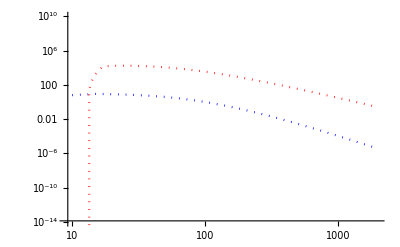

```mathematica
Show[ListLogLogPlot[refdata,PlotRange-> {{9,2000},{10^-14,10^10}},PlotStyle->{Blue,Dotted},Joined-> True],ListLogLogPlot[refdata2,PlotStyle->{Red,Dotted},Joined->True]]
```

```mathematica
fileWrite=OpenWrite["Ine_DM_XSect_Data_Chi_160-Triangle"] ;
Write[fileWrite,dataapp]
Close[fileWrite]
```

Ine_DM_XSect_Data_Chi_0.160-0.025-0.04

```mathematica
vtest=√((8 40 10^-9)/160)299792458/10^3+10^-5;
```

```mathematica
instepdelta=(Log10[100]-Log10[1 10^-3])/100;
instepmphi=(Log10[50]-Log10[1])/100;
inputdelta=Table[10^x,{x,Log10[ 40],Log10[50],instepdelta}]
inputmphi=Table[10^x,{x,Log10[10/10],Log10[15/10],instepmphi}]
```

{40,40 10^(1/20)}

{1,2^(1/100) 5^(1/50),2^(1/50) 5^(1/25),2^(3/100) 5^(3/50),2^(1/25) 5^(2/25),2^(1/20) 5^(1/10),2^(3/50) 5^(3/25),2^(7/100) 5^(7/50),2^(2/25) 5^(4/25),2^(9/100) 5^(9/50),2^(1/10) 5^(1/5)}

```mathematica
datatest=Table[{i,j,Sigmacalc[160,j 10^-3,i 10^-6,60]},{i,inputdelta},{j,inputmphi}]
```

```mathematica
fileread=OpenRead["Ine_DM_XSect_mx-40_mphi-delta_60"];
testread=Read[fileread];
Close[fileread]
```

Ine_DM_XSect_mx-40_mphi-delta_60

```mathematica
testapp=testread;
```

```mathematica
(*For[i=1,i≤ Length[datatest],i++,
testapp=Append[testapp,Extract[datatest,i]];
];*)
```

```mathematica
deltamphi={};
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤Length[Extract[testapp,i]],j++,
If[1≤ Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1]≤ 5,
deltamphi=Append[deltamphi,{Extract[Extract[Extract[testapp,i],j],1],Extract[Extract[Extract[testapp,i],j],2]}];
];
 ];
];
```

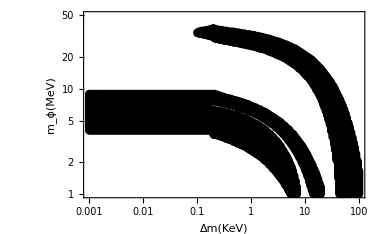

```mathematica
ListLogLogPlot[deltamphi,Frame-> True,FrameTicks->Automatic,FrameLabel->{"Δm(KeV)","m_ϕ(MeV)","m_x = 40 GeV    ,    1 ≤ σ/m_x[cm^2/g] ≤ 5    ,    v = 60 km/s"}, PlotRange-> {{10^-3,100},{1,50}},PlotStyle->{Thick,Black,PointSize[0.0146]}]
```

```mathematica
mydata=10.^{{-8.015151289954603*^-8,1.898173841977281},{-8.015151289954603*^-8,1.9131820640816781},{-8.015151289954603*^-8,1.9131820640816781},{-8.015151289954603*^-8,1.9496746589245626},{-8.015151289954603*^-8,1.9496746589245626},{-8.015151289954603*^-8,1.9508054153844832},{-8.015151289954603*^-8,1.9508054153844832},{-8.015151289954603*^-8,1.9788687347988705},{-8.015151289954603*^-8,1.9788687347988705},{-8.015151289954603*^-8,1.994185345028701},{-8.015151289954603*^-8,1.994185345028701},{-8.015151289954603*^-8,2.0034369887916856},{-8.015151289954603*^-8,2.0034369887916856},{-8.015151289954603*^-8,2.009244965154004},{-8.015151289954603*^-8,2.009244965154004},{-8.015151289954603*^-8,2.0192675792305708},{-8.015151289954603*^-8,2.0192675792305708},{-8.015151289954603*^-8,2.032836656749615},{-8.015151289954603*^-8,2.032836656749615},{-8.015151289954603*^-8,2.0447609975996843},{-8.015151289954603*^-8,2.0447609975996843},{-8.015151289954603*^-8,2.0560685621988877},{-8.015151289954603*^-8,2.0560685621988877},{-8.015151289954603*^-8,2.1087001356060897},{-8.015151289954603*^-8,2.1087001356060897},{-8.015151289954603*^-8,2.1150734901983683},{-8.015151289954603*^-8,2.1150734901983683},{-8.015151289954603*^-8,2.138819375856696},{-8.015151289954603*^-8,2.138819375856696},{-8.015151289954603*^-8,2.1422116452364572},{-8.015151289954603*^-8,2.1422116452364572},{-8.015151289954603*^-8,2.299592385249009},{-8.015151289954603*^-8,2.299592385249009},{-0.05982018492993129,2.2925251573745067},{-0.05982018492993129,2.2925251573745067},{-0.08015158462400289,2.2900580523710445},{-0.08015158462400289,2.2900580523710445},{-0.12022733686024789,2.2851238423641194},{-0.12022733686024789,2.2851238423641194},{-0.14901221554165237,2.281423184858925},{-0.14901221554165237,2.281423184858925},{-0.16030308909649293,2.2799583412631192},{-0.16030308909649293,2.2799583412631192},{-0.20037884133273798,2.2746129470889502},{-0.20037884133273798,2.2746129470889502},{-0.23822381439177015,2.2695245430193087},{-0.23822381439177015,2.2695245430193087},{-0.2587704647082043,2.2665948558276967},{-0.2587704647082043,2.2665948558276967},{-0.27835827134320507,2.2637422656674433},{-0.27835827134320507,2.2637422656674433},{-0.31435404587375804,2.2583840219880478},{-0.31435404587375804,2.2583840219880478},{-0.3741056618177885,2.2489653346571203},{-0.3741056618177885,2.2489653346571203},{-0.38588574133254416,2.247063607883618},{-0.38588574133254416,2.247063607883618},{-0.4007576025139632,2.2445965028801553},{-0.4007576025139632,2.2445965028801553},{-0.4214314463799753,2.24111428696381},{-0.4214314463799753,2.24111428696381},{-0.45681082140103535,2.2349465244551534},{-0.45681082140103535,2.2349465244551534},{-0.4809091069864533,2.2305134451520567},{-0.4809091069864533,2.2305134451520567},{-0.49194559344213795,2.2284575243158375},{-0.49194559344213795,2.2284575243158375},{-0.5209848592226983,2.2230350331103104},{-0.5209848592226983,2.2230350331103104},{-0.5610606114589434,2.2149912428386043},{-0.5610606114589434,2.2149912428386043},{-0.5962051676192441,2.2074871317864053},{-0.5962051676192441,2.2074871317864053},{-0.6412121159314335,2.197207527605311},{-0.6412121159314335,2.197207527605311},{-0.6568471384103203,2.1934297730687593},{-0.6568471384103203,2.1934297730687593},{-0.6812878681676785,2.187287709570555},{-0.6812878681676785,2.187287709570555},{-0.6977251884208258,2.18291887779359},{-0.6977251884208258,2.18291887779359},{-0.7068048510368501,2.180451772790127},{-0.7068048510368501,2.180451772790127},{-0.73083464778788,2.1737700300724168},{-0.73083464778788,2.1737700300724168},{-0.7614393726401686,2.164634031856469},{-0.7614393726401686,2.164634031856469},{-0.7717714025135756,2.161331709013292},{-0.7717714025135756,2.161331709013292},{-0.8015151248764136,2.15125769691582},{-0.8015151248764136,2.15125769691582},{-0.8120819736105798,2.1474542433688155},{-0.8120819736105798,2.1474542433688155},{-0.8267190159312396,2.1418004610692134},{-0.8267190159312396,2.1418004610692134},{-0.8415908771126587,2.13594108668599},{-0.8415908771126587,2.13594108668599},{-0.8572846043067351,2.1293107419891837},{-0.8572846043067351,2.1293107419891837},{-0.870630142893219,2.1231943775014326},{-0.870630142893219,2.1231943775014326},{-0.8816666293489037,2.1178489833272636},{-0.8816666293489037,2.1178489833272636},{-0.8867152348552275,2.115330480302896},{-0.8867152348552275,2.115330480302896},{-0.8988866791379153,2.1087001356060897},{-0.8988866791379153,2.1087001356060897},{-0.9146978157623713,2.099448491843105},{-0.9146978157623713,2.099448491843105},{-0.9217423815851488,2.0949254660034238},{-0.9217423815851488,2.0949254660034238},{-0.9406844363530613,2.0809452043171355},{-0.9406844363530613,2.0809452043171355},{-0.9463200890112833,2.0764221784774537},{-0.9463200890112833,2.0764221784774537},{-0.9618181338213938,2.0611055682476236},{-0.9618181338213938,2.0611055682476236},{-0.9638532306146406,2.058741259285972},{-0.9638532306146406,2.058741259285972},{-0.9658883274078873,2.0560685621988877},{-0.9658883274078873,2.0560685621988877},{-0.9810732804036522,2.0307807359133965},{-0.9810732804036522,2.0307807359133965},{-0.9816211910787571,2.029444387369854},{-0.9816211910787571,2.029444387369854},{-0.9869437519226334,2.0034369887916856},{-0.9869437519226334,2.0034369887916856},{-0.9845715749434821,1.981126810654532},{-0.9845715749434821,1.981126810654532},{-1.0018938860576387,1.9752708733354876},{-1.0018938860576387,1.9752708733354876},{-1.0315593354668906,1.9644772889453386},{-1.0315593354668906,1.9644772889453386},{-1.041969638293884,1.9603654472729006},{-1.041969638293884,1.9603654472729006},{-1.0645513854035649,1.9508054153844832},{-1.0645513854035649,1.9508054153844832},{-1.077505559222117,1.9448432449594484},{-1.077505559222117,1.9448432449594484},{-1.082045390530129,1.9426331300605133},{-1.082045390530129,1.9426331300605133},{-1.092220874496363,1.9374419299490606},{-1.092220874496363,1.9374419299490606},{-1.106192596711538,1.9298864208759565},{-1.106192596711538,1.9298864208759565},{-1.122121142766374,1.9201721949248225},{-1.122121142766374,1.9201721949248225},{-1.1331576292220589,1.9126680838726238},{-1.1331576292220589,1.9126680838726238},{-1.1512386815005207,1.898173841977281},{-1.1512386815005207,1.898173841977281},{-1.1576570636946069,1.8922116715522463},{-1.1576570636946069,1.8922116715522463},{-1.162196895002619,1.887585849670754},{-1.162196895002619,1.887585849670754},{-1.1779297586734885,1.866204272974078},{-1.1779297586734885,1.866204272974078},{-1.1863049647072352,1.8455422685700786},{-1.1863049647072352,1.8455422685700786},{-1.1889662451291736,1.8280669414622186},{-1.1889662451291736,1.8280669414622186},{-1.1877138778717908,1.8120307589397115},{-1.1877138778717908,1.8120307589397115},{-1.182547862935087,1.7929106951628764},{-1.182547862935087,1.7929106951628764},{-1.1747988405300318,1.7763605324313148},{-1.1747988405300318,1.7763605324313148},{-1.162196895002619,1.756520896361803},{-1.162196895002619,1.756520896361803},{-1.156013331669292,1.7484000090587386},{-1.156013331669292,1.7484000090587386},{-1.1527879325585533,1.7444630917057542},{-1.1527879325585533,1.7444630917057542},{-1.1562481505300513,1.7402791217556741},{-1.1562481505300513,1.7402791217556741},{-1.1589094309519896,1.7359616879996147},{-1.1589094309519896,1.7359616879996147},{-1.162196895002619,1.7302051096582018},{-1.162196895002619,1.7302051096582018},{-1.1706895104667447,1.698800918884959},{-1.1706895104667447,1.698800918884959},{-1.1704938280827788,1.6876475483484719},{-1.1704938280827788,1.6876475483484719},{-1.1692414608253965,1.678395904585487},{-1.1692414608253965,1.678395904585487},{-1.162196895002619,1.6561919595543237},{-1.162196895002619,1.6561919595543237},{-1.1557785128085327,1.643445250369767},{-1.1557785128085327,1.643445250369767},{-1.1506124978718293,1.6350159749412696},{-1.1506124978718293,1.6350159749412696},{-1.1386593691163136,1.6180620590816313},{-1.1386593691163136,1.6180620590816313},{-1.1438810238633978,1.610961701157509},{-1.1438810238633978,1.610961701157509},{-1.1495166765216198,1.59903736030744},{-1.1495166765216198,1.59903736030744},{-1.1535868701081133,1.5823844015340673},{-1.1535868701081133,1.5823844015340673},{-1.1544087361207707,1.572156195373879},{-1.1544087361207707,1.572156195373879},{-1.1501428601503108,1.5455834185657502},{-1.1501428601503108,1.5455834185657502},{-1.1441158427241571,1.529752828126865},{-1.1441158427241571,1.529752828126865},{-1.1348013612473733,1.5130998693534923},{-1.1348013612473733,1.5130998693534923},{-1.122121142766374,1.4950077659947665},{-1.122121142766374,1.4950077659947665},{-1.1150765769435962,1.4863728984826476},{-1.1150765769435962,1.4863728984826476},{-1.1067796438634363,1.4771212547196628},{-1.1067796438634363,1.4771212547196628},{-1.1020832666482514,1.471981452629116},{-1.1020832666482514,1.471981452629116},{-1.0928470581250544,1.4629354009497528},{-1.0928470581250544,1.4629354009497528},{-1.082045390530129,1.4524245056745841},{-1.082045390530129,1.4524245056745841},{-1.06936517204913,1.4411426400858334},{-1.06936517204913,1.4411426400858334},{-1.0491707500238343,1.4244896813124606},{-1.0491707500238343,1.4244896813124606},{-1.041969638293884,1.4186303069292368},{-1.041969638293884,1.4186303069292368},{-1.031246243652545,1.4104066235843613},{-1.031246243652545,1.4104066235843613},{-1.0192704817538232,1.4016689600304315},{-1.0192704817538232,1.4016689600304315},{-1.0018938860576387,1.3890250468876855},{-1.0018938860576387,1.3890250468876855},{-0.9770030868171584,1.3718581079052583},{-0.9770030868171584,1.3718581079052583},{-0.9618181338213938,1.3617840958077863},{-0.9618181338213938,1.3617840958077863},{-0.9464570666800596,1.3516843846998612},{-0.9464570666800596,1.3516843846998612},{-0.9217423815851488,1.336059386344598},{-0.9217423815851488,1.336059386344598},{-0.9130149472602633,1.3306882931599762},{-0.9130149472602633,1.3306882931599762},{-0.8943468478299033,1.319226534498056},{-0.8943468478299033,1.319226534498056},{-0.8710019394227546,1.305220573801315},{-0.8710019394227546,1.305220573801315},{-0.8658044662012808,1.3021834295581394},{-0.8658044662012808,1.3021834295581394},{-0.8673035423657963,1.3003634608257482},{-0.8673035423657963,1.3003634608257482},{-0.8815100834417309,1.2668005531744755},{-0.8815100834417309,1.2668005531744755},{-0.8815100834417309,1.266389369007232},{-0.8815100834417309,1.266389369007232},{-0.8770485250873052,1.2200283541504973},{-0.8770485250873052,1.2200283541504973},{-0.8747981776716958,1.2139633876836515},{-0.8747981776716958,1.2139633876836515},{-0.861041706078883,1.1884185712936324},{-0.861041706078883,1.1884185712936324},{-0.8415908771126587,1.1627709588618025},{-0.8415908771126587,1.1627709588618025},{-0.8403776463320692,1.1613318142764493},{-0.8403776463320692,1.1613318142764493},{-0.8188134476190116,1.1386138890362314},{-0.8188134476190116,1.1386138890362314},{-0.8015151248764136,1.1225777065137243},{-0.8015151248764136,1.1225777065137243},{-0.7853908964376117,1.108700240869247},{-0.7853908964376117,1.108700240869247},{-0.770558171732986,1.0967245019982723},{-0.770558171732986,1.0967245019982723},{-0.7614393726401686,1.0895801770924116},{-0.7614393726401686,1.0895801770924116},{-0.7451977347709873,1.077398846137815},{-0.7451977347709873,1.077398846137815},{-0.7282418562003298,1.0651018696361811},{-0.7282418562003298,1.0651018696361811},{-0.715258330024183,1.0560686674620448},{-0.715258330024183,1.0560686674620448},{-0.6812878681676785,1.0333507422218269},{-0.6812878681676785,1.0333507422218269},{-0.6660246422183274,1.023482322207976},{-0.6660246422183274,1.023482322207976},{-0.6476304981255194,1.0118663694833399},{-0.6476304981255194,1.0118663694833399},{-0.6412121159314335,1.0078573238527129},{-0.6412121159314335,1.0078573238527129},{-0.6211742398133109,0.9955217988353999},{-0.6211742398133109,0.9955217988353999},{-0.5905695149610222,0.9771213073512414},{-0.5905695149610222,0.9771213073512414},{-0.5734277381255972,0.9670472952537692},{-0.5734277381255972,0.9670472952537692},{-0.5610606114589434,0.9598258733165503},{-0.5610606114589434,0.9598258733165503},{-0.5283425168598215,0.9411426927174116},{-0.5283425168598215,0.9411426927174116},{-0.5026689880834769,0.9267512468638799},{-0.5026689880834769,0.9267512468638799},{-0.45093056576285595,0.898173947240438},{-0.45093056576285595,0.898173947240438},{-0.44380772698649207,0.8942676976516222},{-0.44380772698649207,0.8942676976516222},{-0.4007576025139632,0.8710100931918965},{-0.4007576025139632,0.8710100931918965},{-0.38699134680195224,0.8636216276867351},{-0.38699134680195224,0.8636216276867351},{-0.36068185027771815,0.8496285164952206},{-0.36068185027771815,0.8496285164952206},{-0.29899297873242386,0.8171578167881894},{-0.29899297873242386,0.8171578167881894},{-0.27254650453941354,0.8033959966907496},{-0.27254650453941354,0.8033959966907496},{-0.25239121899091144,0.7929108004260336},{-0.25239121899091144,0.7929108004260336},{-0.24045459356898302,0.7867173389069244},{-0.24045459356898302,0.7867173389069244},{-0.20037884133273798,0.7660810335133776},{-0.20037884133273798,0.7660810335133776},{-0.1667997442441655,0.7488112984891395},{-0.1667997442441655,0.7488112984891395},{-0.12022733686024789,0.7250140148099065},{-0.12022733686024789,0.7250140148099065},{-0.04196416739303016,0.6851676991029402},{-0.04196416739303016,0.6851676991029402},{-8.015151289954603*^-8,0.6640045639951124},{-8.015151289954603*^-8,0.6640045639951124},{-8.015151289954603*^-8,0.6876476536116292},{-8.015151289954603*^-8,0.6876476536116292},{-8.015151289954603*^-8,0.7929108004260336},{-8.015151289954603*^-8,0.7929108004260336},{-8.015151289954603*^-8,0.8507849719655938},{-8.015151289954603*^-8,0.8507849719655938},{-8.015151289954603*^-8,0.898173947240438},{-8.015151289954603*^-8,0.898173947240438},{-8.015151289954603*^-8,0.9008466443275225},{-8.015151289954603*^-8,0.9008466443275225},{-8.015151289954603*^-8,0.9508055206476402},{-8.015151289954603*^-8,0.9508055206476402},{-8.015151289954603*^-8,0.9518334810657496},{-8.015151289954603*^-8,0.9518334810657496},{-8.015151289954603*^-8,0.9651841169959458},{-8.015151289954603*^-8,0.9651841169959458},{-8.015151289954603*^-8,0.9771213073512414},{-8.015151289954603*^-8,0.9771213073512414},{-8.015151289954603*^-8,1.0034370940548425},{-8.015151289954603*^-8,1.0034370940548425},{-8.015151289954603*^-8,1.0085768961453896},{-8.015151289954603*^-8,1.0085768961453896},{-8.015151289954603*^-8,1.042037007754851},{-8.015151289954603*^-8,1.042037007754851},{-8.015151289954603*^-8,1.0560686674620448},{-8.015151289954603*^-8,1.0560686674620448},{-8.015151289954603*^-8,1.0879354404234367},{-8.015151289954603*^-8,1.0879354404234367},{-8.015151289954603*^-8,1.108700240869247},{-8.015151289954603*^-8,1.108700240869247},{-8.015151289954603*^-8,1.1184658648412864},{-8.015151289954603*^-8,1.1184658648412864},{-8.015151289954603*^-8,1.1294650413150573},{-8.015151289954603*^-8,1.1294650413150573},{-8.015151289954603*^-8,1.1520801705134645},{-8.015151289954603*^-8,1.1520801705134645},{-8.015151289954603*^-8,1.1613318142764493},{-8.015151289954603*^-8,1.1613318142764493},{-8.015151289954603*^-8,1.1937896644782542},{-8.015151289954603*^-8,1.1937896644782542},{-8.015151289954603*^-8,1.2139633876836515},{-8.015151289954603*^-8,1.2139633876836515},{-8.015151289954603*^-8,1.2579086955578291},{-8.015151289954603*^-8,1.2579086955578291},{-8.015151289954603*^-8,1.2665949610908538},{-8.015151289954603*^-8,1.2665949610908538},{-8.015151289954603*^-8,1.2986544766306412},{-8.015151289954603*^-8,1.2986544766306412},{-8.015151289954603*^-8,1.319226534498056},{-8.015151289954603*^-8,1.319226534498056},{-8.015151289954603*^-8,1.3331040001425334},{-8.015151289954603*^-8,1.3331040001425334},{-8.015151289954603*^-8,1.3619639888809552},{-8.015151289954603*^-8,1.3619639888809552},{-8.015151289954603*^-8,1.3718581079052583},{-8.015151289954603*^-8,1.3718581079052583},{-8.015151289954603*^-8,1.3889222508458747},{-8.015151289954603*^-8,1.3889222508458747},{-8.015151289954603*^-8,1.3981738946088593},{-8.015151289954603*^-8,1.3981738946088593},{-8.015151289954603*^-8,1.4244896813124606},{-8.015151289954603*^-8,1.4244896813124606},{-8.015151289954603*^-8,1.4771212547196628},{-8.015151289954603*^-8,1.4771212547196628},{-8.015151289954603*^-8,1.529752828126865},{-8.015151289954603*^-8,1.529752828126865},{-8.015151289954603*^-8,1.5410603927260689},{-8.015151289954603*^-8,1.5410603927260689},{-8.015151289954603*^-8,1.6350159749412696},{-8.015151289954603*^-8,1.6350159749412696},{-8.015151289954603*^-8,1.7207478738115949},{-8.015151289954603*^-8,1.7207478738115949},{-8.015151289954603*^-8,1.7402791217556741},{-8.015151289954603*^-8,1.7402791217556741},{-8.015151289954603*^-8,1.8455422685700786},{-8.015151289954603*^-8,1.8455422685700786},{-8.015151289954603*^-8,1.8776403326255455},{-8.015151289954603*^-8,1.8776403326255455},{-8.015151289954603*^-8,1.8852215407091024},{-8.015151289954603*^-8,1.8852215407091024},{-8.015151289954603*^-8,1.898173841977281},{-8.015151289954603*^-8,1.898173841977281},{-8.015151289954603*^-8,1.8852215407091024},{-8.015151289954603*^-8,1.8776403326255455},{-8.015151289954603*^-8,1.8455422685700786},{-8.015151289954603*^-8,1.7402791217556741},{-8.015151289954603*^-8,1.7207478738115949},{-8.015151289954603*^-8,1.6350159749412696},{-8.015151289954603*^-8,1.5410603927260689},{-8.015151289954603*^-8,1.529752828126865},{-8.015151289954603*^-8,1.4771212547196628},{-8.015151289954603*^-8,1.4244896813124606},{-8.015151289954603*^-8,1.3981738946088593},{-8.015151289954603*^-8,1.3889222508458747},{-8.015151289954603*^-8,1.3718581079052583},{-8.015151289954603*^-8,1.3619639888809552},{-8.015151289954603*^-8,1.3331040001425334},{-8.015151289954603*^-8,1.319226534498056},{-8.015151289954603*^-8,1.2986544766306412},{-8.015151289954603*^-8,1.2665949610908538},{-8.015151289954603*^-8,1.2579086955578291},{-8.015151289954603*^-8,1.2139633876836515},{-8.015151289954603*^-8,1.1937896644782542},{-8.015151289954603*^-8,1.1613318142764493},{-8.015151289954603*^-8,1.1520801705134645},{-8.015151289954603*^-8,1.1294650413150573},{-8.015151289954603*^-8,1.1184658648412864},{-8.015151289954603*^-8,1.108700240869247},{-8.015151289954603*^-8,1.0879354404234367},{-8.015151289954603*^-8,1.0560686674620448},{-8.015151289954603*^-8,1.042037007754851},{-8.015151289954603*^-8,1.0085768961453896},{-8.015151289954603*^-8,1.0034370940548425},{-8.015151289954603*^-8,0.9771213073512414},{-8.015151289954603*^-8,0.9651841169959458},{-8.015151289954603*^-8,0.9518334810657496},{-8.015151289954603*^-8,0.9508055206476402},{-8.015151289954603*^-8,0.9008466443275225},{-8.015151289954603*^-8,0.898173947240438},{-8.015151289954603*^-8,0.8507849719655938},{-8.015151289954603*^-8,0.7929108004260336},{-8.015151289954603*^-8,0.6876476536116292},{-8.015151289954603*^-8,0.6640045639951124},{-0.04196416739303016,0.6851676991029402},{-0.12022733686024789,0.7250140148099065},{-0.1667997442441655,0.7488112984891395},{-0.20037884133273798,0.7660810335133776},{-0.24045459356898302,0.7867173389069244},{-0.25239121899091144,0.7929108004260336},{-0.27254650453941354,0.8033959966907496},{-0.29899297873242386,0.8171578167881894},{-0.36068185027771815,0.8496285164952206},{-0.38699134680195224,0.8636216276867351},{-0.4007576025139632,0.8710100931918965},{-0.44380772698649207,0.8942676976516222},{-0.45093056576285595,0.898173947240438},{-0.5026689880834769,0.9267512468638799},{-0.5283425168598215,0.9411426927174116},{-0.5610606114589434,0.9598258733165503},{-0.5734277381255972,0.9670472952537692},{-0.5905695149610222,0.9771213073512414},{-0.6211742398133109,0.9955217988353999},{-0.6412121159314335,1.0078573238527129},{-0.6476304981255194,1.0118663694833399},{-0.6660246422183274,1.023482322207976},{-0.6812878681676785,1.0333507422218269},{-0.715258330024183,1.0560686674620448},{-0.7282418562003298,1.0651018696361811},{-0.7451977347709873,1.077398846137815},{-0.7614393726401686,1.0895801770924116},{-0.770558171732986,1.0967245019982723},{-0.7853908964376117,1.108700240869247},{-0.8015151248764136,1.1225777065137243},{-0.8188134476190116,1.1386138890362314},{-0.8403776463320692,1.1613318142764493},{-0.8415908771126587,1.1627709588618025},{-0.861041706078883,1.1884185712936324},{-0.8747981776716958,1.2139633876836515},{-0.8770485250873052,1.2200283541504973},{-0.8815100834417309,1.266389369007232},{-0.8815100834417309,1.2668005531744755},{-0.8673035423657963,1.3003634608257482},{-0.8658044662012808,1.3021834295581394},{-0.8710019394227546,1.305220573801315},{-0.8943468478299033,1.319226534498056},{-0.9130149472602633,1.3306882931599762},{-0.9217423815851488,1.336059386344598},{-0.9464570666800596,1.3516843846998612},{-0.9618181338213938,1.3617840958077863},{-0.9770030868171584,1.3718581079052583},{-1.0018938860576387,1.3890250468876855},{-1.0192704817538232,1.4016689600304315},{-1.031246243652545,1.4104066235843613},{-1.041969638293884,1.4186303069292368},{-1.0491707500238343,1.4244896813124606},{-1.06936517204913,1.4411426400858334},{-1.082045390530129,1.4524245056745841},{-1.0928470581250544,1.4629354009497528},{-1.1020832666482514,1.471981452629116},{-1.1067796438634363,1.4771212547196628},{-1.1150765769435962,1.4863728984826476},{-1.122121142766374,1.4950077659947665},{-1.1348013612473733,1.5130998693534923},{-1.1441158427241571,1.529752828126865},{-1.1501428601503108,1.5455834185657502},{-1.1544087361207707,1.572156195373879},{-1.1535868701081133,1.5823844015340673},{-1.1495166765216198,1.59903736030744},{-1.1438810238633978,1.610961701157509},{-1.1386593691163136,1.6180620590816313},{-1.1506124978718293,1.6350159749412696},{-1.1557785128085327,1.643445250369767},{-1.162196895002619,1.6561919595543237},{-1.1692414608253965,1.678395904585487},{-1.1704938280827788,1.6876475483484719},{-1.1706895104667447,1.698800918884959},{-1.162196895002619,1.7302051096582018},{-1.1589094309519896,1.7359616879996147},{-1.1562481505300513,1.7402791217556741},{-1.1527879325585533,1.7444630917057542},{-1.156013331669292,1.7484000090587386},{-1.162196895002619,1.756520896361803},{-1.1747988405300318,1.7763605324313148},{-1.182547862935087,1.7929106951628764},{-1.1877138778717908,1.8120307589397115},{-1.1889662451291736,1.8280669414622186},{-1.1863049647072352,1.8455422685700786},{-1.1779297586734885,1.866204272974078},{-1.162196895002619,1.887585849670754},{-1.1576570636946069,1.8922116715522463},{-1.1512386815005207,1.898173841977281},{-1.1331576292220589,1.9126680838726238},{-1.122121142766374,1.9201721949248225},{-1.106192596711538,1.9298864208759565},{-1.092220874496363,1.9374419299490606},{-1.082045390530129,1.9426331300605133},{-1.077505559222117,1.9448432449594484},{-1.0645513854035649,1.9508054153844832},{-1.041969638293884,1.9603654472729006},{-1.0315593354668906,1.9644772889453386},{-1.0018938860576387,1.9752708733354876},{-0.9845715749434821,1.981126810654532},{-0.9869437519226334,2.0034369887916856},{-0.9816211910787571,2.029444387369854},{-0.9810732804036522,2.0307807359133965},{-0.9658883274078873,2.0560685621988877},{-0.9638532306146406,2.058741259285972},{-0.9618181338213938,2.0611055682476236},{-0.9463200890112833,2.0764221784774537},{-0.9406844363530613,2.0809452043171355},{-0.9217423815851488,2.0949254660034238},{-0.9146978157623713,2.099448491843105},{-0.8988866791379153,2.1087001356060897},{-0.8867152348552275,2.115330480302896},{-0.8816666293489037,2.1178489833272636},{-0.870630142893219,2.1231943775014326},{-0.8572846043067351,2.1293107419891837},{-0.8415908771126587,2.13594108668599},{-0.8267190159312396,2.1418004610692134},{-0.8120819736105798,2.1474542433688155},{-0.8015151248764136,2.15125769691582},{-0.7717714025135756,2.161331709013292},{-0.7614393726401686,2.164634031856469},{-0.73083464778788,2.1737700300724168},{-0.7068048510368501,2.180451772790127},{-0.6977251884208258,2.18291887779359},{-0.6812878681676785,2.187287709570555},{-0.6568471384103203,2.1934297730687593},{-0.6412121159314335,2.197207527605311},{-0.5962051676192441,2.2074871317864053},{-0.5610606114589434,2.2149912428386043},{-0.5209848592226983,2.2230350331103104},{-0.49194559344213795,2.2284575243158375},{-0.4809091069864533,2.2305134451520567},{-0.45681082140103535,2.2349465244551534},{-0.4214314463799753,2.24111428696381},{-0.4007576025139632,2.2445965028801553},{-0.38588574133254416,2.247063607883618},{-0.3741056618177885,2.2489653346571203},{-0.31435404587375804,2.2583840219880478},{-0.27835827134320507,2.2637422656674433},{-0.2587704647082043,2.2665948558276967},{-0.23822381439177015,2.2695245430193087},{-0.20037884133273798,2.2746129470889502},{-0.16030308909649293,2.2799583412631192},{-0.14901221554165237,2.281423184858925},{-0.12022733686024789,2.2851238423641194},{-0.08015158462400289,2.2900580523710445},{-0.05982018492993129,2.2925251573745067},{-8.015151289954603*^-8,2.299592385249009},{-8.015151289954603*^-8,2.1422116452364572},{-8.015151289954603*^-8,2.138819375856696},{-8.015151289954603*^-8,2.1150734901983683},{-8.015151289954603*^-8,2.1087001356060897},{-8.015151289954603*^-8,2.0560685621988877},{-8.015151289954603*^-8,2.0447609975996843},{-8.015151289954603*^-8,2.032836656749615},{-8.015151289954603*^-8,2.0192675792305708},{-8.015151289954603*^-8,2.009244965154004},{-8.015151289954603*^-8,2.0034369887916856},{-8.015151289954603*^-8,1.994185345028701},{-8.015151289954603*^-8,1.9788687347988705},{-8.015151289954603*^-8,1.9508054153844832},{-8.015151289954603*^-8,1.9496746589245626},{-8.015151289954603*^-8,1.9131820640816781}};
```

```mathematica
deltamphia={};
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤Length[Extract[testapp,i]],j++,
If[1≤ Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1]≤ 5,
If[ Im[Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],2],1]]≠ 0 ,
deltamphia=Append[deltamphia,{Extract[Extract[Extract[testapp,i],j],1],Extract[Extract[Extract[testapp,i],j],2]}];
];
];
 ];
];
```

```mathematica
deltamphib={};
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤Length[Extract[testapp,i]],j++,
If[1≤ Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1]≤ 5,
If[ Im[Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],2],1]]== 0 ,
deltamphib=Append[deltamphib,{Extract[Extract[Extract[testapp,i],j],1],Extract[Extract[Extract[testapp,i],j],2]}];
];
];
 ];
];
```

```mathematica
deltamphic={};
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤Length[Extract[testapp,i]],j++,
If[1≤ Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1]≤ 5,
If[ Im[Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],2],1]]== 0 ,
deltamphic=Append[deltamphic,{Extract[Extract[Extract[testapp,i],j],1],Extract[Extract[Extract[testapp,i],j],2],Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],1],1],Extract[Extract[Extract[Extract[Extract[testapp,i],j],3],2],1]}];
];
];
 ];
];
```

```mathematica
dm=40;
condata=Table[{Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3],√((Extract[Extract[deltamphic,i],1] 10^-6)/dm)299792.458},{i,1,Length[deltamphic]}];
```

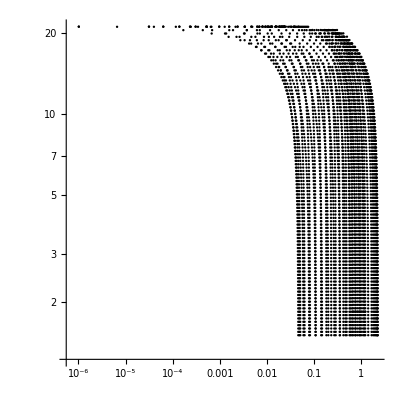

```mathematica
ListLogLogPlot[condata,AspectRatio->1,PlotStyle->{Thick,Black,PointSize[0.0042]}]
```

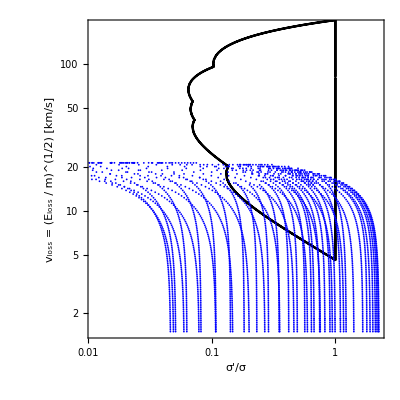

```mathematica
Show[ListLogLogPlot[mydata,Joined-> True,PlotStyle->{Black,PointSize[0.0032]}],ListLogLogPlot[condata,PlotStyle->{Blue,PointSize[0.0032]}],AspectRatio->1,Frame-> True,Axes-> False,FrameLabel->{"σ'/σ","v_loss = (E_loss / m)^(1/2) [km/s]"},PlotRange-> {{-4.5,0.8},{0.4,5.2}}]
```

```mathematica
mydatatest={};
For[i=1,i≤  Length[mydata],i++,
If[Extract[Extract[mydata,i],2]≤  50 ,
If[Extract[Extract[mydata,i],1]<1,
mydatatest=Append[mydatatest,Extract[mydata,i]];
];
];
];
mydatatest=DeleteDuplicates[mydatatest];
mydatatest=DeleteDuplicatesBy[mydatatest,First];
mydataref={Extract[mydatatest,Length[mydatatest]]};
flag=True;
For[i=Length[mydatatest]-1,i≥ 1,i--,
For[j=i+1,j≤ Length[mydatatest] ,j++,
If[Extract[Extract[mydatatest,i],1]>  Extract[Extract[mydatatest,j],1],
flag=False;
];
];
If[flag==True,
mydataref=Append[mydataref,Extract[mydatatest,i]];
];
flag=True;
];
f=Interpolation[mydataref,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
mydatatestg={};
For[i=1,i≤  Length[mydata],i++,
If[Extract[Extract[mydata,i],2]≥   50 ,
If[Extract[Extract[mydata,i],1]<0.9,
mydatatestg=Append[mydatatestg,Extract[mydata,i]];
];
];
];
mydatatestg=DeleteDuplicates[mydatatestg];
mydatatestg=DeleteDuplicatesBy[mydatatestg,First];
mydatarefg={Extract[mydatatestg,1]};
flag=True;
For[i=1,i≤ Length[mydatatestg]-1,i++,
If[Extract[Extract[mydatatestg,i+1],1]>  Extract[Extract[mydatatestg,i],1],
flag=False;
];
If[flag==True,
mydatarefg=Append[mydatarefg,Extract[mydatatestg,i+1]];
];
flag=True;
];
mydatarefg=Drop[mydatarefg,{Length[mydataref]-1,Length[mydataref]}];
g=Interpolation[mydatarefg,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
mydata2={};
For[i=1,i≤  Length[mydata],i++,
If[Extract[Extract[mydata,i],1]<  0.999999,
mydata2=Append[mydata2,Extract[mydata,i]];
];
];
```

```mathematica
a=Log10[4.6];
b=(Log10[6.5]-a)/Log10[0.5];
f2[x_]:=10^a x^b;
alpha=Log10[200];
beta=(Log10[185]-alpha)/Log10[0.5];
f3[x_]:=10^alpha x^beta;
```

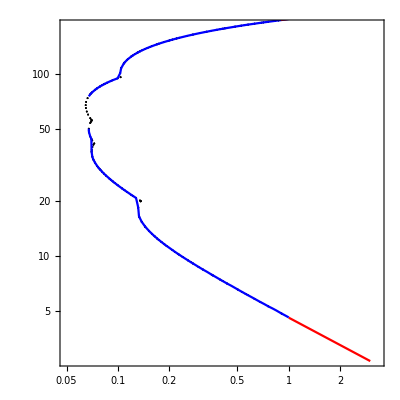

```mathematica
Show[ListLogLogPlot[mydata2,Joined-> False,PlotStyle->{Black,PointSize[0.0032]}],LogLogPlot[{f[x],g[x]},{x,0.0675,1},PlotStyle-> {Blue,Blue}],LogLogPlot[f2[x],{x,1,3},PlotStyle->Red],LogLogPlot[f3[x],{x,0.9,3},PlotStyle->Red],AspectRatio->1,Frame-> True,PlotRange-> {{-3,1.2},{1,5.2}}]
```

```mathematica
parsp={};
For[i=1,i≤ Length[deltamphic],i++,
 
If[ Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3]≤ 0.07,
parsp=Append[parsp,Extract[deltamphic,i]];
]; 
If[0.07< Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3]≤ 1,
If[√((Extract[Extract[deltamphic,i],1] 10^-6)/dm)299792.458<f[Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3]],
parsp=Append[parsp,Extract[deltamphic,i]];
];
 ]; 
If[1< Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3],
If[√((Extract[Extract[deltamphic,i],1] 10^-6)/dm)299792.458<f2[Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3]],
parsp=Append[parsp,Extract[deltamphic,i]]
];
];
];
```

```mathematica
condatab=Table[{Extract[Extract[parsp,i],4]/Extract[Extract[parsp,i],3],√((Extract[Extract[parsp,i],1] 10^-6)/dm)299792.458},{i,1,Length[parsp]}];
```

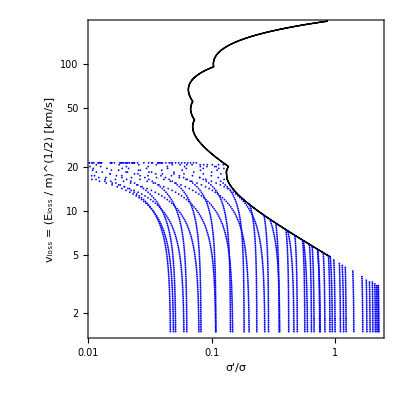

```mathematica
Show[ListLogLogPlot[mydata2,Joined-> True,PlotStyle->{Thick,Black,PointSize[0.0032]}]
,ListLogLogPlot[condatab,PlotStyle->{Thick,Blue,PointSize[0.0032]}],AspectRatio->1,Frame-> True,Axes-> False,FrameLabel->{"σ'/σ","v_loss = (E_loss / m)^(1/2) [km/s]"},PlotRange-> {{-4.5,0.8},{0.4,5.2}}]
```

```mathematica
excl={};
For[i=1,i≤ Length[deltamphic],i++,
 
If[0.07< Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3]≤ 1,
If[√((Extract[Extract[deltamphic,i],1] 10^-6)/dm)299792.458>f[Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3]],
excl=Append[excl,Extract[deltamphic,i]];
];
 ]; 
If[1< Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3],
If[√((Extract[Extract[deltamphic,i],1] 10^-6)/dm)299792.458>f2[Extract[Extract[deltamphic,i],4]/Extract[Extract[deltamphic,i],3]],
excl=Append[excl,Extract[deltamphic,i]]
];
];
];
```

```mathematica
condatac=Table[{Extract[Extract[excl,i],4]/Extract[Extract[excl,i],3],√((Extract[Extract[excl,i],1] 10^-6)/dm)299792.458},{i,1,Length[excl]}];
```

```mathematica
deltamphib2=Table[{Extract[Extract[parsp,i],1],Extract[Extract[parsp,i],2]},{i,1,Length[parsp]}];
deltamphib3=Table[{Extract[Extract[excl,i],1],Extract[Extract[excl,i],2]},{i,1,Length[excl]}];
```

```mathematica
point={};
(* 
   10GeV: 4.5<Extract[Extract[deltamphib3,i],2]<4.6 , 0.048≤ Extract[Extract[deltamphib3,i],1]≤ 0.1
 40GeV: 4.5<Extract[Extract[deltamphib3,i],2]<4.6 , 0.048≤ Extract[Extract[deltamphib3,i],1]≤ 0.053
160GeV: 2.8<Extract[Extract[deltamphib3,i],2]<3 , 0.14≤ Extract[Extract[deltamphib3,i],1]≤ 0.15
*)
For[i=1,i≤ Length[deltamphib3],i++,
If[4.5<Extract[Extract[deltamphib3,i],2]<4.6,
If[0.048≤ Extract[Extract[deltamphib3,i],1]≤ 0.053,
point=Append[point,Extract[deltamphib3,i]];
];
];
];
point=DeleteDuplicates[point]
```

{{1/(10 10^(3/10)),4 2^(7/200) 5^(7/100)}}

```mathematica
pointer={};
(* 10GeV: Null
40GeV: 5<Extract[Extract[deltamphib2,i],2]<5.1 , 0.002≤ Extract[Extract[deltamphib2,i],1]≤ 0.0022
160GeV: 2<Extract[Extract[deltamphib2,i],2]<2.1 , 0.3≤ Extract[Extract[deltamphib2,i],1]≤ 0.33 *)
For[i=1,i≤ Length[deltamphib2],i++,
If[5<Extract[Extract[deltamphib2,i],2]<5.1,
If[0.002≤ Extract[Extract[deltamphib2,i],1]≤ 0.0022,
pointer=Append[pointer,Extract[deltamphib2,i]];
];
];
];
pointer=DeleteDuplicates[pointer]
```

{{1/(100 10^(27/40)),4 2^(3/50) 5^(3/25)}}

```mathematica
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤ Length[Extract[testapp,i]],j++,
If[Extract[Extract[Extract[testapp,i],j],1]== Extract[Extract[point,1],1],
If[Extract[Extract[Extract[testapp,i],j],2]== Extract[Extract[point,1],2],
xsecs=Extract[Extract[testapp,i],j];
];
];
];
];
```

```mathematica
For[i=1,i≤ Length[testapp],i++,
For[j=1,j≤ Length[Extract[testapp,i]],j++,
If[Extract[Extract[Extract[testapp,i],j],1]== Extract[Extract[pointer,1],1],
If[Extract[Extract[Extract[testapp,i],j],2]== Extract[Extract[pointer,1],2],
xsecs2=Extract[Extract[testapp,i],j];
];
];
];
];
```

```mathematica
point2={{Extract[Extract[Extract[xsecs,3],2],1]/Extract[Extract[Extract[xsecs,3],1],1],√((Extract[xsecs,1] 10^-6)/dm)299792.458}};
```

```mathematica
pointer2={{Extract[Extract[Extract[xsecs2,3],2],1]/Extract[Extract[Extract[xsecs2,3],1],1],√((Extract[xsecs2,1] 10^-6)/dm)299792.458}};
```

```mathematica
testflag=False;
For[i=1,i≤Length[condatac],i++,If[{Extract[Extract[Extract[xsecs,3],2],1]/Extract[Extract[Extract[xsecs,3],1],1],√((Extract[xsecs,1] 10^-6)/dm)299792.458}==Extract[condatac,i],
testflag=True;
];
];
testflag
```

True

```mathematica
testflag2=False;
For[i=1,i≤Length[condatab],i++,If[{Extract[Extract[Extract[xsecs2,3],2],1]/Extract[Extract[Extract[xsecs2,3],1],1],√((Extract[xsecs2,1] 10^-6)/dm)299792.458}==Extract[condatab,i],
testflag2=True;
];
];
testflag2
```

True

```mathematica
PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]],{0.015,0},{Thickness[0.0035]}},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{i,min10,max10},{k,9}],1]]];
```

```mathematica
fPowerTicks=Join[{{1,1,{0.015,0},{Thickness[0.0035]}},{2,2,{0.015,0},{Thickness[0.0035]}},{5,5,{0.015,0},{Thickness[0.0035]}},{10,10,{0.015,0},{Thickness[0.0035]}},{20,20,{0.015,0},{Thickness[0.0035]}},{50,50,{0.015,0},{Thickness[0.0035]}}},{{1.5,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{3,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{4,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{6,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{7,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{8,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{9,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{15,Spacer[{0,0}],{0.005,0},{Thickness[0.0035]}},{30,Spacer[{0,0}],{0.005,0},{Thickness[0.0038]}},{40,Spacer[{0,0}],{0.005,0},{Thickness[0.0038]}}}];
```

```mathematica
nonrelavent=ListLogLogPlot[deltamphia,PlotRange->{{  10^-3,100},{  1,50}},PlotStyle->{Darker[Orange,0.05],PointSize[0.0136]},PlotLegends-> Placed[SwatchLegend[{Black}, { Style["m_χ = 40 GeV",Black,FontSize->25]},LegendLayout->"Column",LegendMarkerSize-> {0.1,0.1}],{0.20,0.85}], FrameTicks-> {{fPowerTicks,Automatic},{PowerTicks[True],Automatic}}];
available=ListLogLogPlot[deltamphib2,PlotRange->{{  10^-3,100},{  1,50}},PlotStyle->{Lighter[Blue,0.25],PointSize[0.0146]}];
excluded=ListLogLogPlot[deltamphib3,PlotRange->{{  10^-3,100},{  1,50}},PlotStyle->{Magenta,PointSize[0.0136]}];
avapoint=ListLogLogPlot[pointer,PlotMarkers-> {"★",25},PlotStyle->{Black},PlotRange->{{  10^-3,100},{  1,50}}];excpoint=ListLogLogPlot[point,PlotMarkers-> {"▲",30},PlotStyle->{Black},PlotRange->{{  10^-3,100},{  1,50}}];
```

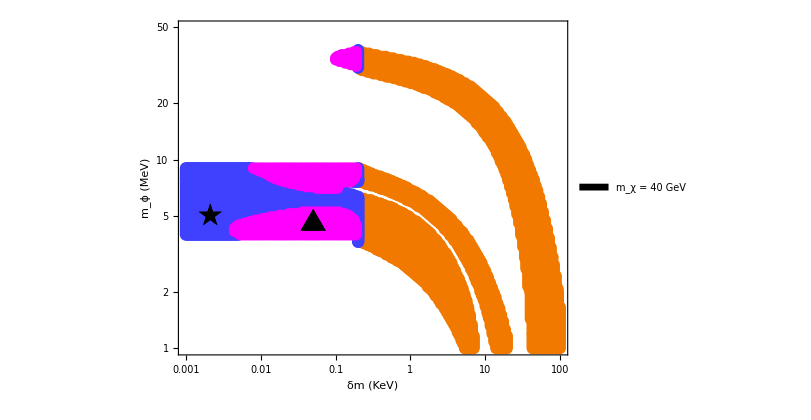

```mathematica
Show[nonrelavent, available , excluded,excpoint,avapoint ,Frame-> True,
FrameLabel->{"δm (KeV)","m_ϕ (MeV)"},FrameStyle-> Directive[Thickness[0.0035],Black,FontSize-> 20],ImageSize-> 600,AspectRatio-> 0.7]
```

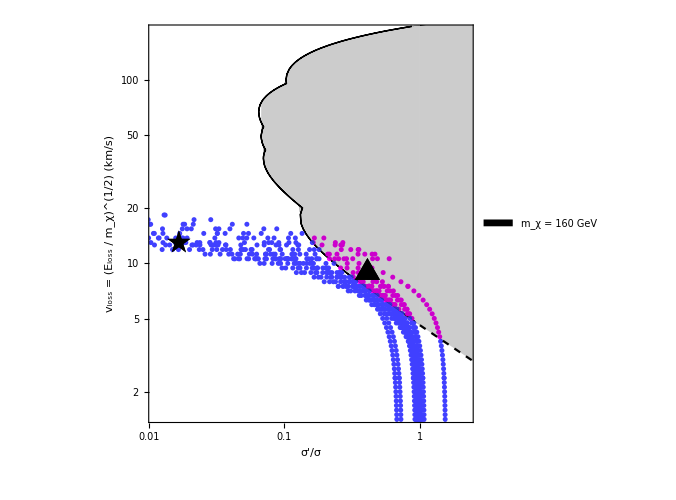

```mathematica
Show[ListLogLogPlot[mydata2,Joined-> True,PlotStyle-> {Thick,Black,PointSize[0.0032]},PlotLegends-> Placed[SwatchLegend[{Black}, { Style["m_χ = 160 GeV",Black,FontSize->25]},LegendLayout->"Column",LegendMarkerSize-> {0.1,0.1}],{0.20,0.95}],FrameTicks-> {{PowerTicks[True],Automatic},{PowerTicks[True],Automatic}}],ListLogLogPlot[condatac,Joined-> False,PlotStyle-> {Thick,Magenta,PointSize[0.0072]}],
ListLogLogPlot[condatab,Joined-> False,PlotStyle->{Thick,Lighter[Blue,0.25],PointSize[0.0072]}],
LogLogPlot[{f2[x],f3[x]},{x,1,3},PlotStyle->{{Black,Dashed},{Black,Dashed}},Filling->{1->{2}}],
LogLogPlot[{f[x],g[x]},{x,0.0675,1},PlotStyle-> {{Black,Thickness[0.0001]},{Black,Thickness[0.0001]}},Filling->{1->{2}}],
ListLogLogPlot[point2,PlotMarkers->{"▲",30},PlotStyle->{Thick,Black}],ListLogLogPlot[pointer2,PlotMarkers->{"★",25},PlotStyle->{Thick,Black}], AspectRatio->1,Frame-> True,Axes-> False,FrameLabel->{"σ'/σ","v_loss = (E_loss / m_χ)^(1/2) (km/s)"},PlotRange-> {{-4.5,0.8},{0.4,5.2}},LabelStyle-> Directive[Black,FontSize-> 20],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 500]
```